```mathematica
SetDirectory[NotebookDirectory[]];
$PlotTheme = "Default";
frameLabelStyle[text_]:= Style[text, FontSize->12,FontColor->Gray];
frameTicksStyle = Directive[FontSize-> 8, FontColor-> Gray];
legendStyle [text_]:= Style[text, FontSize->12, FontColor->Gray];
plotLabelStyle[text_]:= Style[text, FontSize->14, FontColor->Gray];

colorMap = 97;
thesisImages = FileNameJoin[{NotebookDirectory[],"..","..","thesis", "chapters", "img"}];

resultroot = FileNameJoin[{NotebookDirectory[], "results"}];
dataroot = FileNameJoin[{NotebookDirectory[], "data"}];
cm = 72/2.54;
Needs["ErrorBarPlots`"];
```

```mathematica
Needs["DatabaseLink`"];
<<"helpers-scores.wls";
<<"helpers-data.wls";
<<"scores.wls";
```

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx2048m"];
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
```

## Display Tracks

Tracks selected in 2014 used for verification of the manual track selection process. If classification is successful a boundary will be found and an automation can be made.

```mathematica
records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 13
and category = 1
and lda_filter > 0.01
order by source_data_set, source_track_id"
];
```

$Aborted

Simulated tracks used for verification of the classification.

```mathematica
records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 26
order by source_data_set, source_track_id"
];
```

### Helper Functions for Plotting

```mathematica
PlotTrack[i_]:= PlotTrack[i, levelsI];
PlotTrack[i_, levelsIndex_]:=Block[{record, firstFrameid,lastFrameid, track, levels, trackStart, trackEnd, intMin, intMax, plotstart, plotend},
record =records[[i]];
firstFrameid = First@First@record[[dataIntI]];
lastFrameid = First@Last@record[[dataIntI]];
track = record[[dataIntI]];
levels = record[[levelsIndex]];
trackStart = record[[trackStartI]];
trackEnd = record[[trackEndI]];
Block[{low, high},
low = Min[track[[All, 2]]];
high = Max[track[[All, 2]]];
intMin = low - 0.1(high - low);
intMax = high + 0.1(high - low);
];
plotstart = Max[firstFrameid,trackStart-20];
plotend =Min[lastFrameid,trackEnd+20];
Show[
ListLinePlot[
track[[trackStart - firstFrameid+1;; trackEnd-firstFrameid+1, {1, 2}]],
ImageSize->12cm,
AspectRatio->1/5,
Frame-> True,
FrameLabel->(frameLabelStyle/@{"Frame Id", "Intensity"}),
FrameTicksStyle->frameTicksStyle,
FrameTicks->{{Automatic, None}, {Automatic, None}},
PlotRange-> {{plotstart, plotend}, {intMin, intMax}}
],
ListLinePlot[
track[[1;; trackStart-firstFrameid, {1, 2}]],
PlotStyle->Red
],
ListLinePlot[
track[[trackEnd - firstFrameid+2;; -1, {1, 2}]],
PlotStyle->Red
],
Show[
Function[{ranges, mean,color},
ListLinePlot[
Transpose[{#, Table[mean, 2]}]&/@ ranges,
PlotStyle->ColorData[98][color]
]
]@@@ Transpose[{
levels, 
Mean@Flatten[Function[{rangeStart, rangeEnd},
track[[rangeStart-firstFrameid+1;;rangeEnd-firstFrameid+1, 2]]
]@@@ #]&/@levels,
Range[1, Length@levels]
}]
]
]
]
```

```mathematica
GeneratePlots[i_]:= Block[{record, firstFrameid,lastFrameid, track, levels, levelsOld,trackStart, trackEnd, intMin, intMax, plotstart, plotend},
record =records[[i]];
firstFrameid = First@First@record[[dataIntI]];
lastFrameid = First@Last@record[[dataIntI]];
track = record[[dataIntI]];
levels = record[[levelsI]];
levelsOld = record[[levelsOldI]];
trackStart = record[[trackStartI]];
trackEnd = record[[trackEndI]];
Block[{low, high},
low = Min[track[[All, 2]]];
high = Max[track[[All, 2]]];
intMin = low - 0.1(high - low);
intMax = high + 0.1(high - low);
];
plotstart = Max[firstFrameid,trackStart-20];
plotend =Min[lastFrameid,trackEnd+20];

{
Show[
ListLinePlot[
track[[trackStart - firstFrameid+1;; trackEnd-firstFrameid+1, {1, 2}]],
ImageSize->12cm,
AspectRatio->1/5,
PlotLabel->plotLabelStyle@"Refined Levels",
Frame-> True,
FrameLabel->({None,frameLabelStyle@"Intensity"}),
FrameTicksStyle->frameTicksStyle,
FrameTicks->{{Automatic, None}, {Automatic, None}},
PlotRange-> {{plotstart, plotend}, {intMin, intMax}}
],
ListLinePlot[
track[[1;; trackStart-firstFrameid, {1, 2}]],
PlotStyle->Red
],
ListLinePlot[
track[[trackEnd - firstFrameid+2;; -1, {1, 2}]],
PlotStyle->Red
],
Show[
Function[{ranges, mean,color},
ListLinePlot[
Transpose[{#, Table[mean, 2]}]&/@ ranges,
PlotStyle->ColorData[98][color]
]
]@@@ Transpose[{
levels, 
Mean@Flatten[Function[{rangeStart, rangeEnd},
track[[rangeStart-firstFrameid+1;;rangeEnd-firstFrameid+1, 2]]
]@@@ #]&/@levels,
Range[1, Length@levels]
}]
],
ImageSize-> 20cm
],
Show[
ListLinePlot[
track[[trackStart - firstFrameid+1;; trackEnd-firstFrameid+1, {1, 2}]],
ImageSize->12cm,
AspectRatio->1/5,
Frame-> True,
PlotLabel->plotLabelStyle@"2014 Levels",
FrameLabel->(frameLabelStyle/@{"Frame Id", "Intensity"}),
FrameTicksStyle->frameTicksStyle,
FrameTicks->{{Automatic, None}, {Automatic, None}},
PlotRange-> {{plotstart, plotend}, {intMin, intMax}}
],
ListLinePlot[
track[[1;; trackStart-firstFrameid, {1, 2}]],
PlotStyle->Red
],
ListLinePlot[
track[[trackEnd - firstFrameid+2;; -1, {1, 2}]],
PlotStyle->Red
],
Show[
Function[{ranges, mean,color},
ListLinePlot[
Transpose[{#, Table[mean, 2]}]&/@ ranges,
PlotStyle->ColorData[98][color]
]
]@@@ Transpose[{
levelsOld, 
Mean@Flatten[Function[{rangeStart, rangeEnd},
track[[rangeStart-firstFrameid+1;;rangeEnd-firstFrameid+1, 2]]
]@@@ #]&/@levelsOld,
Range[1, Length@levelsOld]
}]
],
ImageSize -> 20cm
],
ListPlot[Transpose@(

Transpose[
Flatten[
track[[#1-firstFrameid+1;;#2-firstFrameid+1,{4, 5}]] &@@@ #,1
]
] - Mean@track[[-10;;-1, {4, 5}]]

)&/@levels,
PlotRange->All,
ImageSize->15cm,
Frame-> True
],
Block[{lvl, imgr, r, fraction},
lvl =1;
imgr = 5;
r=2;
fraction = 0.1;
Row[
MatrixPlot[
ArrayReshape[#, {2imgr+1, 2imgr+1}
][[imgr+1-r;;imgr+1+r,imgr+1-r;;imgr+1+r]], ImageSize->5cm,
FrameTicks->None]&/@TrackLevel[record[[levelsI]][[lvl]], record[[dataImgI]], 2][[Take[#,5]&[
First/@SortBy[Transpose[{Range[1, Length@#], #}]&@FeatureShapeRatios[record[[dataImgI]], 2, r, imgr, record[[levelsI]][[lvl]]], First]
]
]]
]
],
Row[Framed/@{StringTake[record[[datasetNameI]], {-55, -1}], record[[trackIdI]]}],
Grid[{
{"RatioRealPointsL1", RatioRealPointsL1[record]},
{"RatioRealPointsL2",RatioRealPointsL2[record]},
{"FragmentationL1", FragmentationL1[record]},
{"FragmentationL2", FragmentationL2[record]},
{"LongestRangeL1", LongestRangeL1[record]},
{"LongestRangeL2",LongestRangeL2[record]},
{"SignalToNoiseL1", SignalToNoiseL1[record]},
{"SignalToNoiseL2", SignalToNoiseL2[record]},
{"GoesToZero", GoesToZero[record]},
{"StepRatio", record[[scoresI]]["stepratio_lvl12"]}
}],
record[[levelsOldI]]
}
]
```

### Review Tracks

```mathematica
CombiScore1 = {{"sigovermlsig",0.00121106467364977},{"level1points",1.17746656168521*10^-05},{"pos_density_12",8.75913633005609*10^-07},{"level2points",7.76867794554431*10^-07},{"signal_lvl1",-2.0787254661599*10^-10},{"signal_lvl2",-2.3563747755189*10^-12},{"semdr12",0.0038136382683473},{"leveliness",-0.000163848310655005},{"cts_loc_sn_l1",1.31719099154007*10^-05},{"cts_loc_sn_l2",-1.42703953665429*10^-06},{"maxstepfrac",0.000983206748619847},{"dr12",0.00130695872794275},{"ratio_real_points",0.00446874281054202},{"displacement",-0.000276603523032094},{"cts_slm_l1",1.14556868613883*10^-08},{"cts_slm_l2",1.87379556971246*10^-07},{"meanovermlsig",-0.000217673881230429},{"levelrchisq",-0.000153654707356854},{"background",0.000269318614085381},{"shortest_range",1.60905846423149*10^-05}};
i = 1;
Column[{
Row[{
Button["Previous",i=Max[i-1,1]], 
Button["Next",i=Min[i+1,Length[records]]]
}],
Dynamic@i,
Dynamic@ Column@GeneratePlots@i
}
]
```

PreviousNext

The track below has acceptable confidence interval and separation and is published in a paper, however the distance is not real, because stepratio_lvl12 is 2.19.
"20140915_0001_0010_29089cb1-1601-43a1-871c-dc56a18deb6b"3025

Examples of mistakes by 2014 ld:

70  merged segments that shouldn’t have been merged

84  merged segments that shouldn’t have been merged

87  merged segments that shouldn’t have been merged

88  merged segments that shouldn’t have been merged

112 merged segments that shouldn’t have been merged

116 parts of levels that should be excluded

### Export some images for the thesis

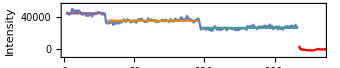

```mathematica
Block[{img},
img = PlotTrack[52, levelsOldI];
Export[FileNameJoin[{thesisImages, "intro-manual-selection-levels.pdf"}], img];
img]
```

```mathematica
Block[{img},
img = Column[{PlotTrack[116, levelsOldI],
PlotTrack[70, levelsOldI],
PlotTrack[112, levelsOldI],
PlotTrack[87, levelsOldI],
PlotTrack[63, levelsOldI]}];
Export[FileNameJoin[{thesisImages, "intro-level-detection-error1.pdf"}], img];
img
];
```

```mathematica
Block[{img},
img = Column[GeneratePlots[63]⟦1;;2⟧];
Export[FileNameJoin[{thesisImages,"classify-smi-newlevel-oldlevel.pdf"}], img];
img
]
```

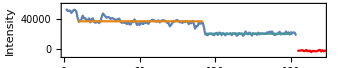
Export
-Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Block[{f, low, high, colorScheme, imgE, feats},
feats = records[[222]][[dataImgI]];
colorScheme = "AlpineColors";
f = Transpose[{feats[[170;;173]], Range[170, 173]}];
low = Min@f;
high = Max@f;
imgE = Column[{PlotTrack[222], 
Row[
ReliefPlot[ArrayReshape[#1, {11, 11}] ,
FrameTicks-> None, 
ColorFunction->colorScheme,
PlotLabel->frameLabelStyle["Frame: " <> ToString[#2]],
ImageSize->3cm]&@@@ f

],
BarLegend[{colorScheme, {low, high}}, LegendLayout->"Row"]
}, 
Alignment->Center];
Column[{
Button["Export",Export[FileNameJoin[{thesisImages, "classify-smi-mistake-goes-to-zero-ex_2.pdf"}], imgE]
],
imgE
}]
]
```

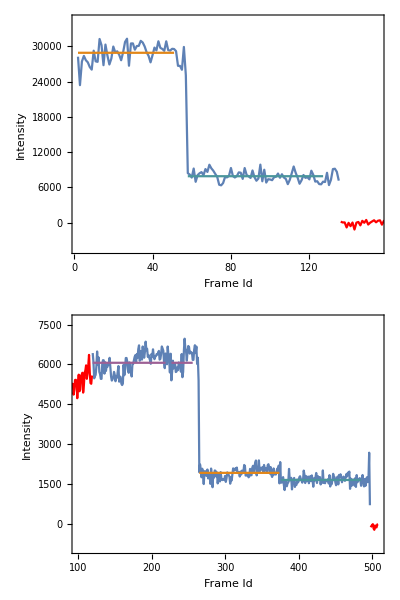
Export
-Graphics-

```mathematica
Block[{img},
img = Column@{PlotTrack[54],PlotTrack[62]};
Column[{
Button["Export",
Export[FileNameJoin[{thesisImages, "classify-smi-mistake-stepratio-ex.pdf"}], img]
],
img
}]
]
```

## Classify Simulated Tracks

### Read Data

```mathematica
records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 138
order by source_data_set, source_track_id"
];
```

```mathematica
data= Function[{uw},Block[{m,s},
m = Mean@Keys@uw;
s = StandardDeviation@Keys@uw;
(Keys@# - m)/s-> Values@#&/@uw]]@(ExtractScores/@ records);
```

```mathematica
hus = Join[Range[1, 10], {15, 20, 25}];
```

```mathematica
<<"classify-nn.wls"
```

### Classify Data

```mathematica
BinarySerialize[Table[classifyTrail[data, hus], 10]]>>"classify-simulated-raw.bin";
```

```mathematica
(BinarySerialize[Table[classifyTrail[#, hus], 10]]&@compressPCA[data, 17])>>"classify-simulated-compressed17.bin";
```

### Plot The Results

```mathematica
evals = Eigenvalues@Covariance@Keys@data ;
```

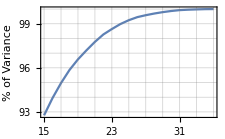

```mathematica
Block[{img}, 
img = ListLinePlot[{#,(Total[evals[[1;;#]]]/Total@evals * 100)}&/@ Range[15, 35],
Frame->True,
FrameTicks->{
{Range[93, 100, 1],None },
{Range[15, 35,2], None}
},
GridLines->{Range[15, 35, 2], Range[93, 100, 1]},
FrameTicksStyle->frameTicksStyle,
PlotStyle->ColorData[colorMap],
ImageSize->8cm,
FrameLabel -> (frameLabelStyle/@{"Number of PC", "% of Variance"})];
Export[FileNameJoin[{thesisImages, "classify-smi-property-pca-simulated.pdf"}], img];
img]
```

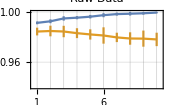
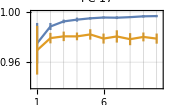

```mathematica
Block[{img},
img = 
Column[{
Row[Function[{res, label},
ErrorListPlot[
Transpose[{Transpose[{Range[1,10], #}]&/@Mean@#, ErrorBar/@#&/@(StandardDeviation@#)}, {3, 1, 2}]&@res[[All, All, 1;;10, 1]],
Joined->True,
PlotLabel->plotLabelStyle@(label),
Frame-> True,
FrameTicksStyle-> frameTicksStyle,
FrameTicks->{{Automatic, None}, {Range[1, 10], None}},
PlotRange->{{0.7,10.3},{0.94, 1.0}},
FrameLabel-> frameLabelStyle/@{"Hidden Units", "F1Score"},
GridLines->{hus, Automatic},
ImageSize->6cm
]
]@@@ Transpose[{
{
BinaryDeserialize[<<"classify-simulated-raw.bin"],
BinaryDeserialize[<<"classify-simulated-compressed17.bin"]
},
{"Raw Data", "PC 17"}}]
],
SwatchLegend[ColorData[colorMap]/@{1, 2}, legendStyle/@{"Training Set", "Testing Set"}, LegendLayout->"Row"]
},

Alignment->Center];
Export[FileNameJoin[{thesisImages,"classify-smi-nn-f1score-simulated.pdf"}], img];
img
]
```

## Classify Tracks NN

Max training rounds used were 1000. This is maybe too little. Try try to repeat the experiment with 5000.

```mathematica
data = BinaryDeserialize@Get@FileNameJoin[{dataroot, "2014-lda_gt_0.01-revised-scores.bin"}];
```

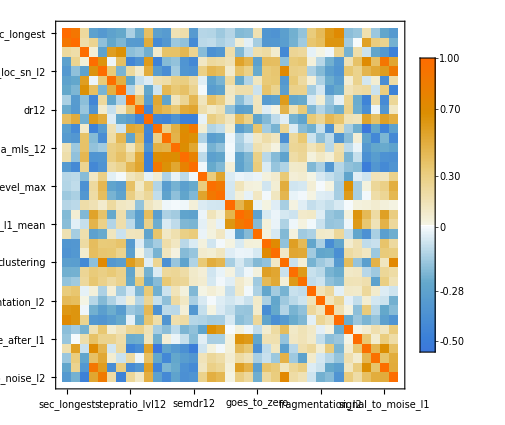

```mathematica
Block[{scoreLabels, img},
scoreLabels = {
"sec_longest",
"sec_most_pts",
"count_sigma_mls_12",
"cts_loc_sn_l1",
"cts_loc_sn_l2",
"cts_slm_l1",
"cts_slm_l2",
"stepratio_lvl12",
"dr12",
"pos_density_12",
"pos_error_1",
"pos_error_2",
"pos_sigma_mls_12",
"pos_sigma_locmean_12",
"semdr12",
"l12_off_level_min",
"l12_off_level_max",
"l12_off_level_mean",
"int_before_after_l1_min",
"int_before_after_l1_max",
"int_before_after_l1_mean",
"goes_to_zero",
"background_l1",
"background_l2",
"clustering",
"feature_shape_l1",
"feature_shape_l2",
"fragmentation_l1",
"fragmentation_l2",
"longest_range_l1",
"longest_range_l2",
"l12_gap",
"frames_before_after_l1",
"ratio_real_point_l1",
"ratio_real_point_l2",
"signal_to_moise_l1",
"signal_to_noise_l2"
};
img = MatrixPlot[Covariance@Standardize@Keys@data,
FrameTicksStyle->frameTicksStyle,
FrameTicks->{
Transpose@{Range[1, 37],scoreLabels},Transpose@{Range[1, 37],Rotate[#, Pi/2]&/@scoreLabels}
},
PlotLegends->Automatic,
ImageSize->15cm
];
Export[FileNameJoin[{thesisImages, "classify-smi-property-correlation.pdf"}], Show[img, ImageSize-> 15cm]];
img
]
```

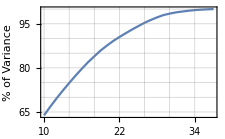

```mathematica
Block[{img},
img = ListLinePlot[
Function[ev,
{#,100 Total[ev[[1;;#]]]/Total[ev]}&/@Range[10, Length@ev]
]@Eigenvalues@Covariance@Standardize@Keys@data,
GridLines->{Range[10, 37, 4],Range[65, 100, 5]},
Frame-> True,
FrameTicks->{{Range[65, 100, 5], None}, {Range[10, 37, 4], None}},
FrameTicksStyle->frameTicksStyle,
PlotStyle->ColorData[colorMap],
ImageSize->8cm,
FrameLabel -> (frameLabelStyle/@{"Number of PC", "% of Variance"})
];
Export[FileNameJoin[{thesisImages, "classify-smi-property-pca.pdf"}], img];
img
]
```

```mathematica
nndir = FileNameJoin[{resultroot, "nn", "2018-10-02_16-05-15"}];
```

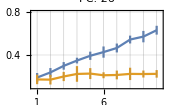
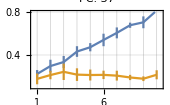

```mathematica
Block[{nndir, img},
nndir = FileNameJoin[{resultroot, "nn", "2018-10-02_16-05-15"}];

img = Column[{
Row[
ErrorListPlot[
Transpose[{Transpose[{Range[1, 10], #}]&/@Mean@#, ErrorBar/@#&/@(StandardDeviation@#)}, {3, 1, 2}]&@BinaryDeserialize[Get[FileNameJoin[{nndir, "2014-lda_lt_0.01-revised_scores-pca_" <> ToString[#] <> ".bin"}]]][[All, All, All, 1]],
Joined->True,
PlotLabel->plotLabelStyle@("PC: "<>ToString[#]),
Frame-> True,
FrameTicksStyle-> frameTicksStyle,
FrameTicks->{{Automatic, None}, {Range[1, 10], None}},
PlotRange->{{0.7, 10.3},{0.1, 0.8}},
FrameLabel-> frameLabelStyle/@{"Hidden Units", "F1Score"},
GridLines->{Range[1, 10], Automatic},
ImageSize->6cm
]&/@{26, 37}
],
SwatchLegend[ColorData[colorMap]/@{1, 2}, legendStyle/@{"Training Set", "Testing Set"}, LegendLayout->"Row"]
},

Alignment->Center];
Export[FileNameJoin[{thesisImages, "classify-smi-nn-f1score.pdf"}],img];
img
]
```

```mathematica
TransformLabelledData[data_, trf_]:= #1->#2 &@@@ Transpose[{trf@Keys@data, Values@data}];
```

```mathematica
sdata= TransformLabelledData[data, Standardize];
```

```mathematica
evect = Transpose@Part[#, 1;;26]&@Eigenvectors@Covariance@Keys@sdata;
```

```mathematica
{trainFull, testFull} = TakeDrop[RandomSample@sdata, Floor[0.7 Length@sdata]];
```

```mathematica
trainProj = TransformLabelledData[trainFull, #.evect&];
testProj = TransformLabelledData[testFull, #.evect&];
```

```mathematica
netFull = NetTrain[
NetInitialize[
NetChain[{LinearLayer[3], Tanh, LinearLayer[2], SoftmaxLayer[]}, "Input"-> 37, "Output"-> NetDecoder[{"Class", {no, yes}}]],
Method->{"Xavier", "FactorType"-> "Mean", "Distribution"-> "Normal"}
],
trainFull,
MaxTrainingRounds->1000,
TargetDevice-> "CPU",
LossFunction->CrossEntropyLossLayer["Index"]];
```

```mathematica
netProj = NetTrain[
NetInitialize[
NetChain[{LinearLayer[5], Tanh, LinearLayer[2], SoftmaxLayer[]}, "Input"-> 26, "Output"-> NetDecoder[{"Class", {no, yes}}]],
Method->{"Xavier", "FactorType"-> "Mean", "Distribution"-> "Normal"}
],
trainProj,
MaxTrainingRounds->1000,
TargetDevice-> "CPU",
LossFunction->CrossEntropyLossLayer["Index"],
Method-> "ADAM"];
```

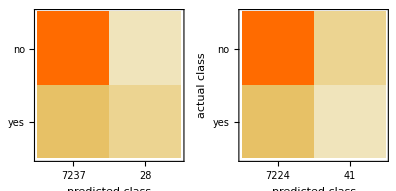

```mathematica
Block[{img},
img = GraphicsRow[{ClassifierMeasurements[netProj, testProj,"ConfusionMatrixPlot"],ClassifierMeasurements[netFull, testFull, "ConfusionMatrixPlot"]
}, ImageSize->14cm];
Export[FileNameJoin[{thesisImages, "classify-smi-nn-test-confusion.pdf"}], img];
img
]
```

## Track Selection Mistakes

```mathematica
data = BinaryDeserialize@Get@FileNameJoin[{dataroot, "2014-lda_gt_0.01-revised-scores.bin"}];
p = Keys@Select[data, Values@#===yes&];
```

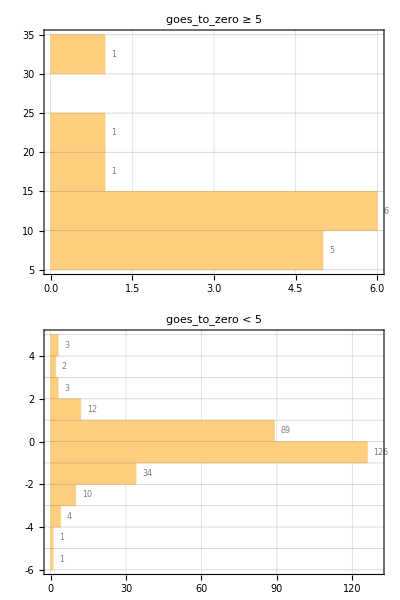

```mathematica
Block[{
goesToZeroI,
img },
goesToZeroI= 22;
img = Column[
{Histogram[
Select[p⟦All,goesToZeroI⟧,#≥ 5&],{5, 35, 5},
AspectRatio->1/6,
Frame-> True,
FrameTicks->{{Range[5, 35, 5], None},{Automatic, None} },
GridLines->{Automatic, Range[5, 35, 5]},
BarOrigin->Left,
FrameTicksStyle->frameTicksStyle,
LabelingFunction->After,
LabelStyle->frameTicksStyle,
PlotLabel->plotLabelStyle@"goes_to_zero ≥ 5" ,
ImageSize->12cm
],
Histogram[
Select[p⟦All,goesToZeroI⟧,#< 5&],{-6, 5, 1},
AspectRatio->1/3,
Frame-> True,
FrameTicks->{{Range[-6, 5, 1], None},{Automatic, None} },
PlotRange->{{0,130} , {-6, 5}},
GridLines->{Automatic, Range[-6, 5, 1]},
BarOrigin->Left,
FrameTicksStyle->frameTicksStyle,
LabelingFunction->After,
LabelStyle->frameTicksStyle,
PlotLabel->plotLabelStyle@"goes_to_zero < 5",
ImageSize->12cm
]
}];
Export[FileNameJoin[{thesisImages, "classify-smi-mistake-goes-to-zero.pdf"}], img];
img
]
```

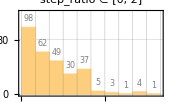
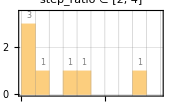

```mathematica
Block[{img, stepratio},
stepratio = 8;
img = Row@{Histogram[
p⟦All,stepratio⟧, {0, 2, 0.2},
LabelingFunction->Above,
LabelStyle->frameTicksStyle,
ImageSize-> 6cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Automatic, None},{Range[0, 2, 0.4], None}},
GridLines->{Range[0, 2, 0.2],Automatic},
PlotRange->{{0, 2}, {0, 120}},
PlotLabel->plotLabelStyle@"step_ratio ∈ [0, 2]"
],
Histogram[
p⟦All,stepratio⟧, {2, 4, 0.2},
LabelingFunction->Above,
LabelStyle->frameTicksStyle,
ImageSize->6cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Automatic, None},{Range[2, 4, 0.4], None}},
GridLines->{Range[2, 4, 0.2],Automatic},
PlotRange->{{2, 4},{0, 3.5}},
PlotLabel->plotLabelStyle@"step_ratio ∈ [2, 4]"
]};
Export[FileNameJoin[{thesisImages, "classify-smi-mistake-stepratio.pdf"}], img];
img]
```

```mathematica
N@Length@Select[p[[All, stepratio]], #> 0.3&]/Length@p
```

0.531773

## Thesis Plots

### Simulations

#### Analysable Tracks

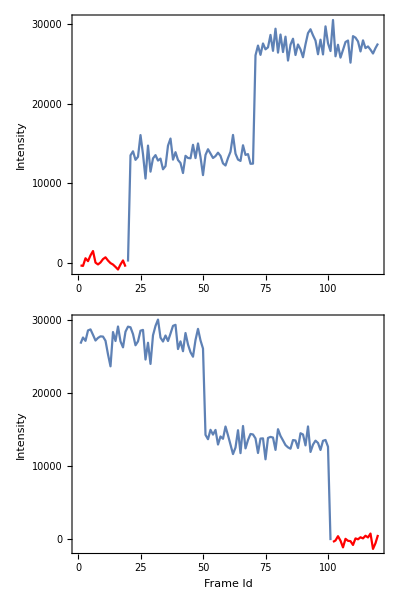

```mathematica
Block[{l1first, l1last, img},
l1first = First[
SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 138
and category = 1
and levels_order = 'L1First'
order by source_data_set, source_track_id
limit 1"
]
];
l1last = First[
SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 138
and category = 1
and levels_order = 'L1Last'
order by source_data_set, source_track_id
limit 2"
]
];
img = Column[{
ListLinePlot[
{
Transpose[{Range[20, 120],l1first[[dataIntI]][[20;;-1, 2]]}],
Transpose[{Range[1, 19], l1first[[dataIntI]][[1;;19, 2]]}]
},
AspectRatio->1/8,
ImageSize -> 12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 30000, 10000], None}, {Automatic, None}},
PlotStyle->{colorMap[colorMap][1], RGBColor[1, 0, 0]},
FrameLabel-> {None,frameLabelStyle["Intensity"]}
]
,
ListLinePlot[{
Transpose[{Range[1, 101],l1last[[dataIntI]][[1;; 101, 2]]}],
Transpose[{Range[102, 120], l1last[[dataIntI]][[102;;120,2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 30000, 10000], None}, {Automatic, None}},
PlotStyle->{colorMap[colorMap][1], RGBColor[1, 0, 0]},
FrameLabel-> (frameLabelStyle/@{"Frame Id","Intensity"})
]
}];
Export[FileNameJoin[{thesisImages, "simulations-track-classification-analysable.pdf"}], img];
img]
```

#### Step Ratio

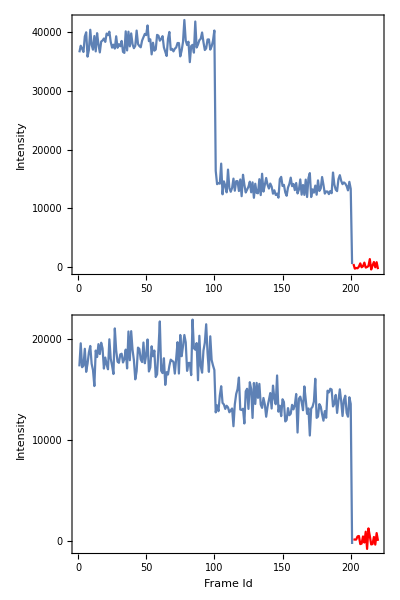

```mathematica
Block[{img, records},
records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 138
and category = 0
and source_data_set like '%stepratio%batch_00001%'
order by source_data_set, source_track_id"];
img = Column[{
ListLinePlot[{
Transpose[{Range[1, 201],records[[3]][[dataIntI]][[1;; 201, 2]]}],
Transpose[{Range[202, 220], records[[3]][[dataIntI]][[202;;220,2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 40000, 10000], None}, {Automatic, None}},
PlotStyle->{colorMap[colorMap][1], RGBColor[1, 0, 0]},
FrameLabel-> {None,frameLabelStyle["Intensity"]}
],
ListLinePlot[{
Transpose[{Range[1, 201],records[[-1]][[dataIntI]][[1;; 201, 2]]}],
Transpose[{Range[202, 220], records[[-1]][[dataIntI]][[202;;220,2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 40000, 10000], None}, {Automatic, None}},
PlotStyle->{colorMap[colorMap][1], RGBColor[1, 0, 0]},
FrameLabel-> (frameLabelStyle/@{"Frame Id","Intensity"})
]}];
Export[FileNameJoin[{thesisImages, "simulations-track-classification-stepratio.pdf"}], img];
img
]
```

#### Additional Fluorophore

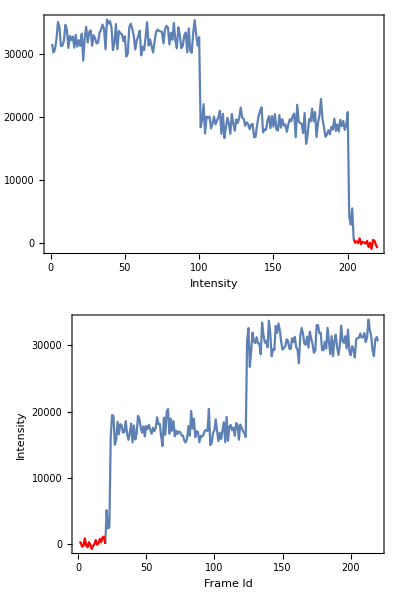

```mathematica
Block[{img, records},
records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 138
and category = 0
and source_data_set like '%add_flfr%batch_00001%'
order by source_data_set, source_track_id"];
img = Column[{
ListLinePlot[{
Transpose[{Range[1, 204],records[[3]][[dataIntI]][[1;; 204, 2]]}],
Transpose[{Range[204, 220], records[[3]][[dataIntI]][[204;;220,2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 40000, 10000], None}, {Automatic, None}},
PlotStyle->{colorMap[colorMap][1], RGBColor[1, 0, 0]},
FrameLabel-> {frameLabelStyle["Intensity"]}
],
ListLinePlot[{
Transpose[{Range[20, 220],records[[-1]][[dataIntI]][[20;; 220, 2]]}],
Transpose[{Range[1, 20], records[[-1]][[dataIntI]][[1;;20,2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 40000, 10000], None}, {Automatic, None}},
PlotStyle->{colorMap[colorMap][1], RGBColor[1, 0, 0]},
FrameLabel-> (frameLabelStyle/@{"Frame Id","Intensity"})
]}];
Export[FileNameJoin[{thesisImages, "simulations-track-classification-addflfr.pdf"}], img];
img
]
```

#### Extrapolated Intensity

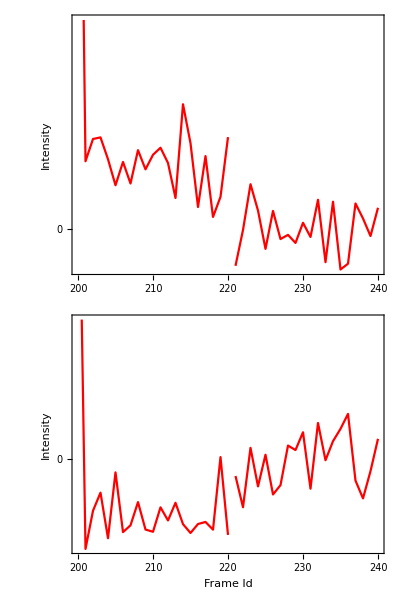

```mathematica
Block[{img, records},
records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 138
and category = 0
and source_data_set like '%extr_int1%batch_00001%'
order by source_data_set, source_track_id"];
img = Column[{
ListLinePlot[{
Transpose[{Range[200, 220],records[[3]][[dataIntI]][[200;; 220, 2]]}],
Transpose[{Range[221, 240], records[[3]][[dataIntI]][[221;;240,2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 40000, 10000], None}, {Automatic, None}},
PlotStyle-> RGBColor[1, 0, 0],
FrameLabel-> {None,frameLabelStyle["Intensity"]}
],
ListLinePlot[{
Transpose[{Range[200, 220],records[[-1]][[dataIntI]][[200;; 220, 2]]}],
Transpose[{Range[221, 240], records[[-1]][[dataIntI]][[221;;240,2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 40000, 10000], None}, {Automatic, None}},
PlotStyle->RGBColor[1, 0, 0],
FrameLabel-> (frameLabelStyle/@{"Frame Id","Intensity"})
]}];
Export[FileNameJoin[{thesisImages, "simulations-track-classification-extrint.pdf"}], img];
img
]
```

#### Interruptions

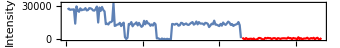

```mathematica
Block[{img, record},
record = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 138
and category = 0
and source_data_set like '%interruption%batch_00001%'
order by source_data_set, source_track_id
limit 1"];
img =
ListLinePlot[
{
Transpose[{Range[1, 137],record[[1]][[dataIntI]][[1;; 137, 2]]}],
Transpose[{Range[138, 200], record[[1]][[dataIntI]][[138;; 200, 2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 40000, 10000], None}, {Automatic, None}},
PlotStyle-> {ColorData[colorMap][1], RGBColor[1, 0, 0]},
FrameLabel-> (frameLabelStyle/@{"Frame Id","Intensity"})
];
Export[FileNameJoin[{thesisImages, "simulations-track-classification-interruptions.pdf"}], img];
img
]
```

#### Level 1/2 Gap

```mathematica
Clear[records]
```

```mathematica
Block[{img, records},
records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 138
and category = 0
and source_data_set like '%lvl12_gap%batch_00001%'
order by source_data_set, source_track_id"];
img =
ListLinePlot[
{
Transpose[{Range[1, 137],record[[1]][[dataIntI]][[1;; 137, 2]]}],
Transpose[{Range[138, 200], record[[1]][[dataIntI]][[138;; 200, 2]]}]
},
AspectRatio->1/8,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameTicks-> {{Range[0, 40000, 10000], None}, {Automatic, None}},
PlotStyle-> {ColorData[colorMap][1], RGBColor[1, 0, 0]},
FrameLabel-> (frameLabelStyle/@{"Frame Id","Intensity"})
];
Export[FileNameJoin[{thesisImages, "simulations-track-classification-interruptions.pdf"}], img];
img
]
```